# Postelje Ameriških Bolnicah

## pridobivanje podatkov

Podatke sem pridobil iz Wolfram data repository

```mathematica
podatki = ResourceData["Hospital Beds Per US State"]
```

## Alabama

Najprej si bomo pogledali, kaj se dogaja v Alabami.

```mathematica
Alabama = Select[podatki,#["Location"]== LinguisticAssistant&]
```

```mathematica
NeprofitnePosteljeAlabama = %[[1]]["NonProfitBedsPer1000Inhabitants"]
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Null⟦1⟧[NonProfitBedsPer1000Inhabitants]

```mathematica
TimeSeries[…]
```

TimeSeries[…]

```mathematica
DateListPlot[NeprofitnePosteljeAlabama, PlotLabel->"Neprofitne postelje na 1000 prebivalcev v Alabami", PlotTheme->"Web", ImageSize->Large]
```

DateListPlot::ldata: Null⟦1⟧[NonProfitBedsPer1000Inhabitants] is not a valid dataset or list of datasets.

DateListPlot[Null⟦1⟧[NonProfitBedsPer1000Inhabitants],PlotLabel→Neprofitne postelje na 1000 prebivalcev v Alabami,PlotTheme→Web,ImageSize→Large]

```mathematica
DateListPlot[Differences[NeprofitnePosteljeAlabama], PlotLabel->"Razlike v številu neprofitnih postelj v Alabami na 1000 prebivalcev med leti", PlotTheme->"Web", ImageSize->Large]
```

DateListPlot::ldata: Differences[Null⟦1⟧[NonProfitBedsPer1000Inhabitants]] is not a valid dataset or list of datasets.

DateListPlot[Differences[Null⟦1⟧[NonProfitBedsPer1000Inhabitants]],PlotLabel→Razlike v številu neprofitnih postelj v Alabami na 1000 prebivalcev med leti,PlotTheme→Web,ImageSize→Large]

## Kentucky

```mathematica
Kentucky = Select[podatki,#["Location"]== LinguisticAssistant&]

KvotaNa1000PrebivalcevKentucky = {3.96*10^6, 3.98*10^6, 4.06*10^6,4.09*10^6,4.11*10^6,4.14*10^6,4.18*10^6,4.21*10^6,4.25*10^6,4.28*10^6,4.31*10^6,4.33*10^6,4.37*10^6,4.38*10^6,4.40*10^6,4.41*10^6,4.42*10^6,4.43*10^6,4.45*10^6,4.46*10^6} / 1000
```

{3960.,3980.,4060.,4090.,4110.,4140.,4180.,4210.,4250.,4280.,4310.,4330.,4370.,4380.,4400.,4410.,4420.,4430.,4450.,4460.}

```mathematica
TotalBedsPer1000Kentucky = %[[1]]["TotalBedsPer1000Inhabitants"]
```

TimeSeries[…]

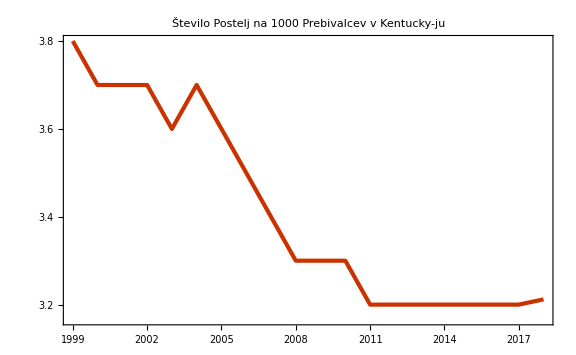

```mathematica
g1 = DateListPlot[TotalBedsPer1000Kentucky, PlotLabel->"Število Postelj na 1000 Prebivalcev v Kentucky-ju", PlotTheme->"Web", ImageSize->Large]
```

## Florioda

```mathematica
Florida = Select[podatki,#["Location"]== LinguisticAssistant&]
```

TimeSeries[…]

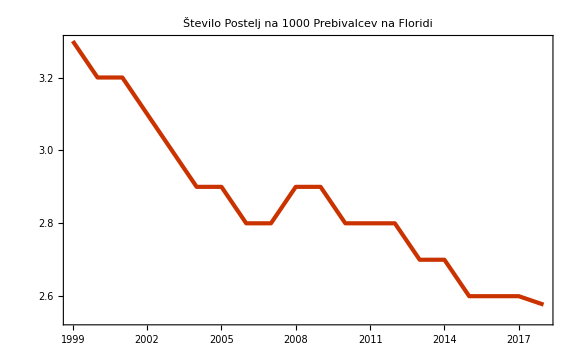

-Graphics-

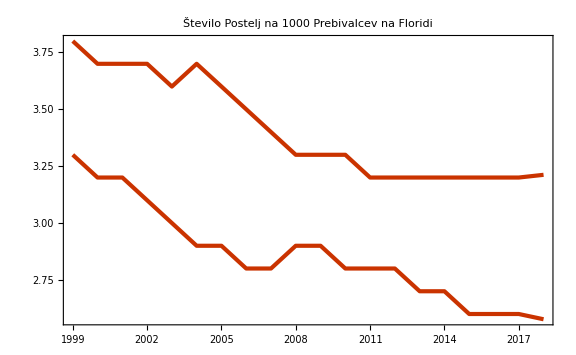

```mathematica
TotalBedsPer1000Florida = %[[1]]["TotalBedsPer1000Inhabitants"]
g2 = DateListPlot[TotalBedsPer1000Florida, PlotLabel->"Število Postelj na 1000 Prebivalcev na Floridi", PlotTheme->"Web", ImageSize->Large]
g1 = DateListPlot[TotalBedsPer1000Kentucky, PlotLabel->"Število Postelj na 1000 Prebivalcev v Kentucky-ju", PlotTheme->"Web", ImageSize->Large]
Show[g2,g1, PlotRange->All]
```

Graf prikazuje Skupno število postelj v zdravstvu na 1000 Prebivalcev v Kentuckyju in Floridi.

## Vse Države

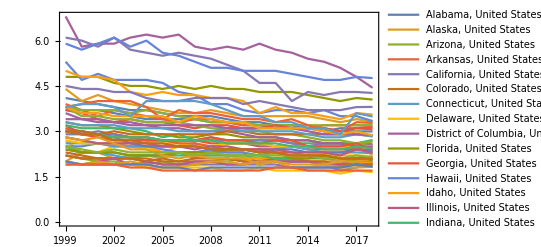

-Graphics-

```mathematica
DateListPlot[ResourceData[ResourceObject["Hospital Beds Per US State"]][GroupBy["Location"], Total, #TotalBedsPer1000Inhabitants &]]
GeoRegionValuePlot[
 DeleteCases[
  Normal[{#["Location"], #["TotalBedsPer1000Inhabitants"][
       "LastValue"]} & /@ ResourceData[ResourceObject["Hospital Beds Per US State"]]], {Entity["Country", "UnitedStates"], _}]]
```

## Aplikacija v oblaku

```mathematica
grafPostelj[drzava_] := DateListPlot[Select[podatki,#["Location"]==drzava&][All,"NonProfitBedsPer1000Inhabitants"], PlotLabel->"Prikaz postelj na 1000 prebivalcev.", AxesLabel->{"Leto","Število postelj"},PlotStyle->Orange, ImageSize->{800,550}];
```

```mathematica
obrazec = FormPage["drzava"-> "AdministrativeDivision",grafPostelj[#drzava]&,AppearanceRules-><|"Title" -> "Graf neprofitnih postelj na 1000 prebivalcev.","Description"-> "Vnesite drzavo (izbirate lahko med: Kentucky, United States; Florida, United States; Alabama, United States;...)","SubmitLabel" -> "Potrdi"|>]
```

```mathematica
CloudDeploy[obrazec,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/83feae48-bd09-4e33-ab99-eaac3104dd36]